```mathematica
(*
4.0 Explore the posibility of position C
assuming:
 lc is still 2.4cm
Rmax is 3cm larger
Rmin is still 3.5cm；
5.0 Use it to fix zeeman slower
*)
```

```mathematica
ClearAll["Global`*"]
(*AWG constants*)
d14=1.6277*10^-3; (*m*)
d15=1.4495*10^-3;
d16=1.2908*10^-3;
rd16=1.30*10^-3;
d17=1.1495*10^-3;
d18=1.0237*10^-3;
rd18=1.07*10^-3;
d19=0.9116*10^-3;
d20=0.8118*10^-3;
d21=0.7229*10^-3;
d22=0.6438*10^-3;

(*Parameters*)
(*X is the distance from coil(close end) to atoms*)

(*lc is the hight of the coil cylinder*)
lc=10*10^-2; (*m or 3cm*)
L=1 ;(* total layers or 3 layers*)
μ0=1.25663706212*10^-6; (*H/m*)
R0=2.9*10^-2 ;(*m*)
(*Rmax=7.5*10^-2; (*m*)*)
ρ=1.68*10^(-8); (* Ω*m *)

(*calculated parameters*)
n[d_]:=1/d; (*winds/m*)
R[j_,d_]:=R0+d/2+(j-1)*d*(√3)/2 (*m*) 

(*taking into consideration the shape of the cross section of the cord*)

B[X_,i_,d_]:=i*∑_(j=1)^L ∫_X^(X+lc) μ0/2*(R[j,d]^2*n[d])/((R[j,d]^2+x^2)^(3/2))ⅆx
B[0,1,d14]
n[d14]*lc
```

0.000369925

61.4364

```mathematica
coilPosition=35 ;(*cm down the slower*)
f[i_]:=10000*B[(i-coilPosition)/i,1,d14];
result=Array[f,77,0]
```

Power::infy: Infinite expression 1/0 encountered.

{0,7.09261×10^-9,6.23494×10^-8,2.31939×10^-7,6.07968×10^-7,1.31771×10^-6,2.53633×10^-6,4.50445×10^-6,7.55271×10^-6,0.0000121364,0.0000188847,0.0000286713,0.0000427181,0.0000627468,0.0000912073,0.000131625,0.000189141,0.000271363,0.000389755,0.000561937,0.000815648,0.00119577,0.00177731,0.00269065,0.0041732,0.00668309,0.0111712,0.0198073,0.0382221,0.08398,0.229817,0.943682,4.58761,6.72119,6.4612,3.72845,1.00057,0.344914,0.162448,0.0921373,0.0587377,0.0405441,0.02964,0.0226286,0.0178706,0.0145012,0.0120313,0.0101684,0.00872902,0.00759402,0.00668309,0.0059407,0.00532746,0.00481483,0.00438174,0.00401235,0.00369458,0.0034191,0.00317858,0.00296723,0.00278042,0.0026144,0.00246612,0.00233306,0.00221317,0.00210469,0.00200618,0.00191642,0.00183435,0.0017591,0.00168989,0.00162608,0.00156709,0.00151242,0.00146165,0.0014144,0.00137033}

```mathematica
SetDirectory[NotebookDirectory[]];
Export["fixingCoil.csv",result]
```

fixingCoil.csv

```mathematica
R[L,d14]
```

0.0635005

```mathematica
(*Garbage*)
(*Now calculate power/heat P=I^2 Ω *)
ClearAll[L,Ω,Current,LayerNum,P,dused,L,in,Resistance,Pow,Vol]
L[m_,d_]:=∑_(j=1)^m 2*π*R[j,d]*lc/d
Ω[m_,d_]:=ρ*L[m,d]/(π*((d-(rd16-d16))/2)^2)
Current[m_,d_]:=Btarg/Cfn[d,m]
LayerNum[d_]:=Floor[(Rmax-(R0+d))/(d*(√3)/2)+1]
P[d_]:=With[{b=LayerNum[d]},(Current[b,d])^2*Ω[b,d]];

(*choose coil diameter*)
dused=rd16;

(*Calculate*)
Num=LayerNum[dused]
"Layers"
L[Num,dused]
"m Cord Length"  
in=Current[Num,dused] 
"A current"
Resistance=Ω[Num,dused] 
"Ω resistance"
Pow=in^2*Resistance
"w power"
Vol=in*Resistance
"V needed"
```

35

Layers

222.439

m Cord Length

5.38726

A current

2.8557

Ω resistance

82.8797

w power

15.3844

V needed

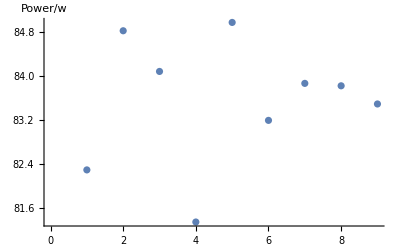

```mathematica
ListPlot[Map[P,{d14,d15,d16,d17,d18,d19,d20,d21,d22}],AxesLabel->"Power/w"]
```

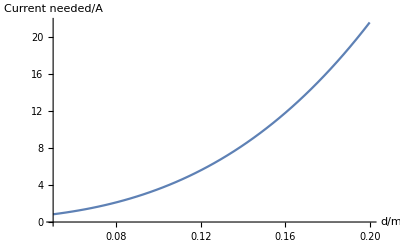

```mathematica
ClearAll[X]
Plot[Current[10,d18],{X,5*10^-2,20*10^-2},AxesLabel->{"d/m","Current needed/A"}]
```

```mathematica
R[15,d18]
```

0.0479236